Practical 1
Make a geometric plot to show that the nth roots of unity are equally spaced points that lie on the unit circle C1(0)={z:|z|<1} and form the vertices off a regular polygon with n sides, for n = 4, 5, 6 ,7 ,8.

```mathematica
For z = 5;
```

Set::write: Tag Times in For z is Protected.

```mathematica
Solve[z^5==1,z]
```

{{z→1},{z→-(-1)^(1/5)},{z→(-1)^(2/5)},{z→-(-1)^(3/5)},{z→(-1)^(4/5)}}

```mathematica
roots= ComplexExpand[Solve[z^5==1,z]]
```

{{z→1},{z→-1/4-(√5)/4-ⅈ √(5/8-(√5)/8)},{z→-1/4+(√5)/4+ⅈ √(5/8+(√5)/8)},{z→-1/4+(√5)/4-ⅈ √(5/8+(√5)/8)},{z→-1/4-(√5)/4+ⅈ √(5/8-(√5)/8)}}

```mathematica
z/.roots
```

{1,-1/4-(√5)/4-ⅈ √(5/8-(√5)/8),-1/4+(√5)/4+ⅈ √(5/8+(√5)/8),-1/4+(√5)/4-ⅈ √(5/8+(√5)/8),-1/4-(√5)/4+ⅈ √(5/8-(√5)/8)}

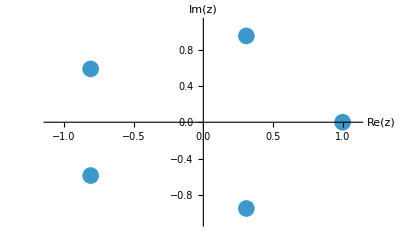

```mathematica
rootPlot=ListPlot[{Re[z],Im[z]}/.roots, PlotRange->{{-1.1,1.1},{-1.1,1.1}},
AxesLabel->{"Re(z)","Im(z)"},PlotStyle->PointSize[0.03]]
```

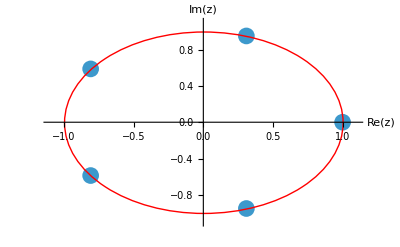

```mathematica
Show[rootPlot, Graphics[{Red,Circle[{0,0},1]}]]
```

```mathematica
For z= 4;
```

Set::write: Tag Times in For z is Protected.

```mathematica
Solve[z^4==1,z]
```

{{z→-1},{z→-ⅈ},{z→ⅈ},{z→1}}

```mathematica
roots1= ComplexExpand[Solve[z^4==1,z]]
```

{{z→-1},{z→-ⅈ},{z→ⅈ},{z→1}}

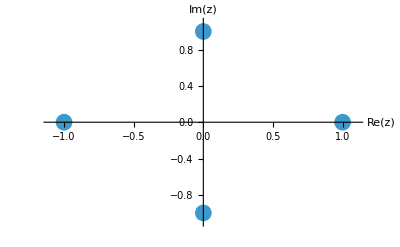

```mathematica
rootPlot1=ListPlot[{Re[z],Im[z]}/.roots1, PlotRange->{{-1.1,1.1},{-1.1,1.1}},
AxesLabel->{"Re(z)","Im(z)"},PlotStyle->PointSize[0.03]]
```

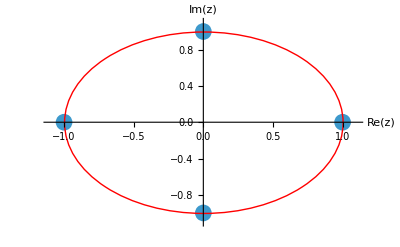

```mathematica
Show[rootPlot1, Graphics[{Red,Circle[{0,0},1]}]]
```

```mathematica
For z= 6;
```

Set::write: Tag Times in For z is Protected.

```mathematica
Solve[z^6==1,z]
```

{{z→-1},{z→1},{z→-(-1)^(1/3)},{z→(-1)^(1/3)},{z→-(-1)^(2/3)},{z→(-1)^(2/3)}}

```mathematica
roots2= ComplexExpand[Solve[z^6==1,z]]
```

{{z→-1},{z→1},{z→-1/2-(ⅈ √3)/2},{z→1/2+(ⅈ √3)/2},{z→1/2-(ⅈ √3)/2},{z→-1/2+(ⅈ √3)/2}}

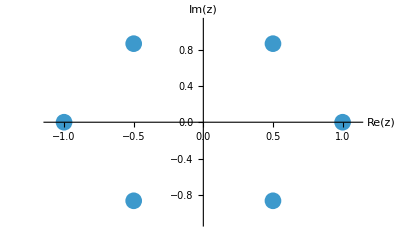

```mathematica
rootPlot2=ListPlot[{Re[z],Im[z]}/.roots2, PlotRange->{{-1.1,1.1},{-1.1,1.1}},
AxesLabel->{"Re(z)","Im(z)"},PlotStyle->PointSize[0.03]]
```

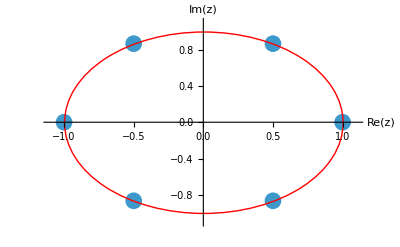

```mathematica
Show[rootPlot2, Graphics[{Red,Circle[{0,0},1]}]]
```

```mathematica
For z=7;
```

Set::write: Tag Times in For z is Protected.

```mathematica
Solve[z^7==1,z]
```

{{z→1},{z→-(-1)^(1/7)},{z→(-1)^(2/7)},{z→-(-1)^(3/7)},{z→(-1)^(4/7)},{z→-(-1)^(5/7)},{z→(-1)^(6/7)}}

```mathematica
roots3= ComplexExpand[Solve[z^7==1,z]]
```

{{z→1},{z→-Cos[π/7]-ⅈ Sin[π/7]},{z→ⅈ Cos[(3 π)/14]+Sin[(3 π)/14]},{z→-ⅈ Cos[π/14]-Sin[π/14]},{z→ⅈ Cos[π/14]-Sin[π/14]},{z→-ⅈ Cos[(3 π)/14]+Sin[(3 π)/14]},{z→-Cos[π/7]+ⅈ Sin[π/7]}}

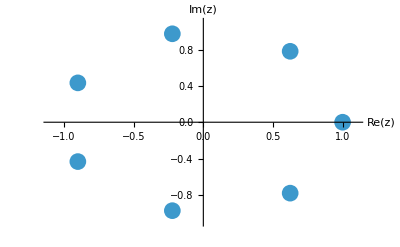

```mathematica
rootPlot3=ListPlot[{Re[z],Im[z]}/.roots3, PlotRange->{{-1.1,1.1},{-1.1,1.1}},
AxesLabel->{"Re(z)","Im(z)"},PlotStyle->PointSize[0.03]]
```

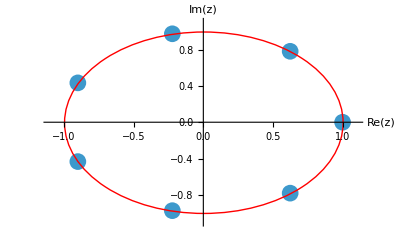

```mathematica
Show[rootPlot3, Graphics[{Red,Circle[{0,0},1]}]]
```

```mathematica
For z=8;
```

Set::write: Tag Times in For z is Protected.

```mathematica
Solve[z^8==1,z]
```

{{z→-1},{z→-ⅈ},{z→ⅈ},{z→1},{z→-(-1)^(1/4)},{z→(-1)^(1/4)},{z→-(-1)^(3/4)},{z→(-1)^(3/4)}}

```mathematica
roots4= ComplexExpand[Solve[z^8==1,z]]
```

{{z→-1},{z→-ⅈ},{z→ⅈ},{z→1},{z→-(1+ⅈ)/(√2)},{z→(1+ⅈ)/(√2)},{z→(1-ⅈ)/(√2)},{z→-(1-ⅈ)/(√2)}}

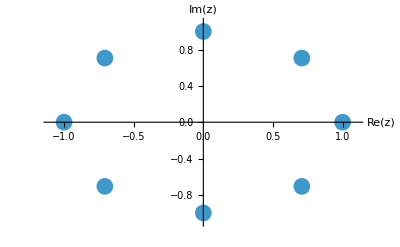

```mathematica
rootPlot4=ListPlot[{Re[z],Im[z]}/.roots4, PlotRange->{{-1.1,1.1},{-1.1,1.1}},
AxesLabel->{"Re(z)","Im(z)"},PlotStyle->PointSize[0.03]]
```

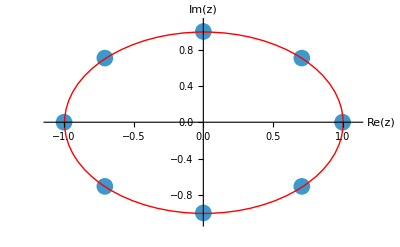

```mathematica
Show[rootPlot4, Graphics[{Red,Circle[{0,0},1]}]]
```

```mathematica
ClearAll
```

ClearAll

Practical 2
Find all the solutions of the equation z^3=8i and represent these geometrically.

```mathematica
Solve[z^3==8*I,z]
```

{{z→-2 ⅈ},{z→2 (-1)^(1/6)},{z→2 (-1)^(5/6)}}

```mathematica
roots5=ComplexExpand[Solve[z^3==8*I,z]]
```

{{z→-2 ⅈ},{z→ⅈ+√3},{z→ⅈ-√3}}

```mathematica
z/.roots5
```

{-2 ⅈ,ⅈ+√3,ⅈ-√3}

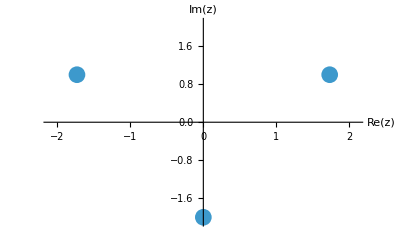

```mathematica
rootPlot5=ListPlot[{Re[z],Im[z]}/.roots5, PlotRange->{{-2.1,2.1},{-2.1,2.1}},
AxesLabel->{"Re(z)","Im(z)"},PlotStyle->PointSize[0.03]]
```

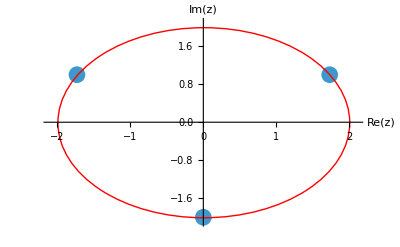

```mathematica
Show[rootPlot5, Graphics[{Red,Circle[{0,0},2]}]]
```

Practical 3
Write parametric equations and make a parametric plot for an ellipse centered at the origin with horizontal major-axis of 4 units and vertical minor-axis of 2 units.
Show the effect of rotation of this ellipse by an angle of Pi/6 radians and shifting of the center from (0,0) to (2,i) by making a parametric plot.

```mathematica
Clear[r,s,t];
```

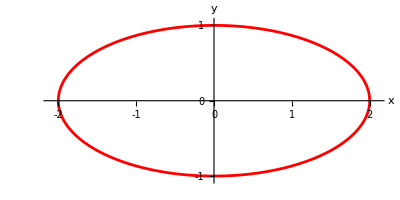

s[t]=2 Cos[t]+ⅈ Sin[t]for 0<=t<=2*Pi

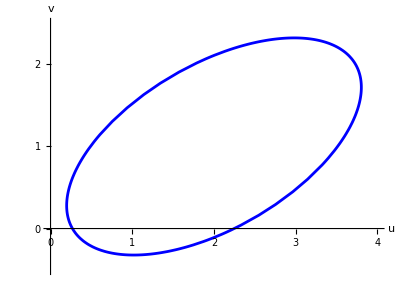

r[t]=(2+ⅈ)+ⅇ^((ⅈ π)/6) (2 Cos[t]+ⅈ Sin[t]) for 0<=t<=2*Pi

```mathematica
s[t_]=2Cos[t]+I*Sin[t];
r[t_]=s[t]*Exp[I*Pi/6]+(2+I);
ParametricPlot[{Re[s[t]],Im[s[t]]},{t,0,2*Pi},PlotStyle->Red,
PlotRange->{{-2.1,2.1},{-1.05,1.05}},AspectRatio->1/2,
Ticks->{Range[-2,2,1],Range[-2,2,1]},AxesLabel->{"x","y"}]
Print["s[t]=",s[t],"for 0<=t<=2*Pi"];
ParametricPlot[{Re[r[t]],Im[r[t]]},{t,0,2*Pi},PlotStyle->Blue,
PlotRange->{{0,4},{-0.5,2.5}},AspectRatio->3/4,
Ticks->{Range[0,4,1],Range[0,3,1]},AxesLabel->{"u","v"}]
Print["r[t]=",r[t]," for 0<=t<=2*Pi"]
```

Practical 4
Show that the image of the open disk D I ={z:|z+1+i<1|} under the linear transformation w= f(z)=(3-4i)z+6+2i is the open disk D2={w:|w+1-3i|<5}. Procedure: If w=f(z) then w=(3-4i)z+6+2i this impliesz=(w-6-2i)/(3-4i)
Now |z+1+i|<1 can be written as |(w-6-2i)/(3-4i)+1+i|<1
Plotting of f(D I) is equivalent to plotting of all those f(z) for which |z+1+i|<1 or in terms of w we can say that it is equivalent to plotting of w for which |(w-6-2i)/(3-4i)+1+i|<1.

```mathematica
z=x+ⅈ*y
Solve[w1==(3-4ⅈ)z1+6+2ⅈ,z1]
```

x+ⅈ y

{{z1→1/25 (-10+3 w1+2 ⅈ (-15+2 w1))}}

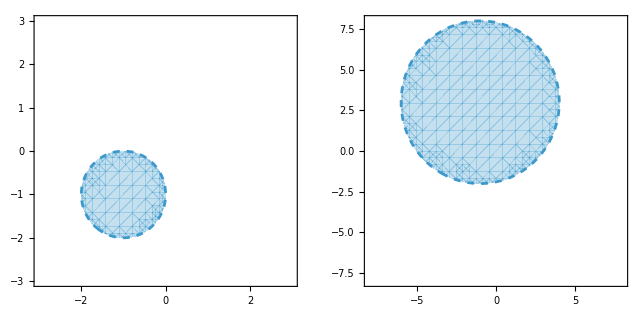

```mathematica
A1=RegionPlot[Abs[z+1+ⅈ]<1,
{x,-3,3},{y,-3,3},BoundaryStyle->Dashed, Axes->True];
A2=RegionPlot[Abs[((z-6-2ⅈ)/(3-4ⅈ))+1+ⅈ]<1,{x,-8,8},
{y,-8,8},BoundaryStyle->Dashed, Axes->True];
GraphicsRow[{A1,A2}]
```

Practical 5
Show that the image of the right half plane Re(z)=x>1 under the linear transformation w=(-1+i)z-2+3i is the half plane v>u+7, where u=Re(w), etc. Plot the map. Procedure= If w=f(z)=(-1+i)z-2+3i, then z=(w+2-3i)/(-1+i)={(u+2)+i(v-3)}/(-1+i=[(-u+v-5)+i(-u-v+1)]/2, so that Re(z)=x>1 => v>u+7.

```mathematica
z=x+ⅈ*y
Solve[w1==(-1+ⅈ)z1-2+3ⅈ,z1]
```

x+ⅈ y

{{z1→1/2 (-5+ⅈ (1-w1)-w1)}}

```mathematica
A3=RegionPlot[Re[z]>1,{x,-5,5},{y,-5,5}, Axes->True];
A4= RegionPlot[Re[(z+2-3ⅈ)/(-1+ⅈ)]>1,{x,-7,7},{y,-7,7}Axes->True];
GraphicsRow[{A1,A2}]
```

-Graphics-

Practical 6

Show that the image of the right half-plane A = {z: Re z ≥ 1/ 2}  under the mapping  𝑤 =𝑓(z) =1/z is the closed disk  𝐷_1(1)bar = {w: |w – 1| ≤ 1} in the w- plane.

x+ⅈ y

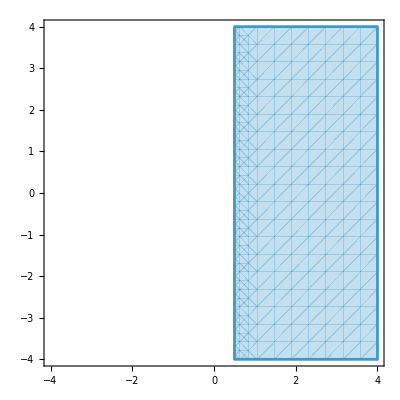

```mathematica
z=x+ⅈ*y
A1=RegionPlot[Re[z]≥1/2,{x,-4,4},{y,-4,4},Axes->True]
```

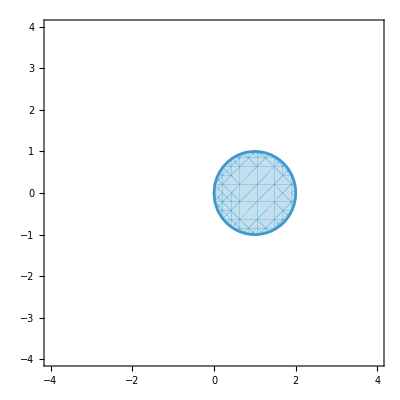

```mathematica
A11=RegionPlot[Re[1/z]≥1/2,{x,-4,4},{y,-4,4},Axes->True]
```

Practical 7

Make a plot of the vertical lines x = a, for 𝑎 = −1,−1/2,1/2,1 and the horizontal lines  y = b, for 𝑏 = −1,−1/2,1/2 , 1. Find the plot of this grid under the mapping 𝑓(𝑧) = 1/z.

x+ⅈ y

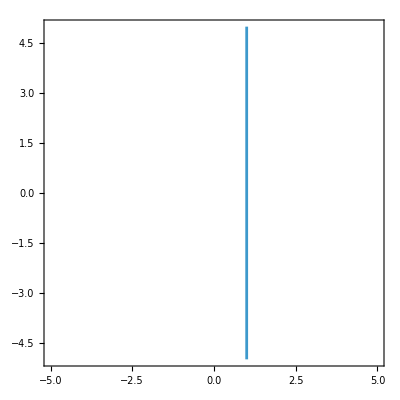

```mathematica
z=x+ⅈ*y
A2=ContourPlot[Re[z]==1,{x,-5,5},{y,-5,5}]
```

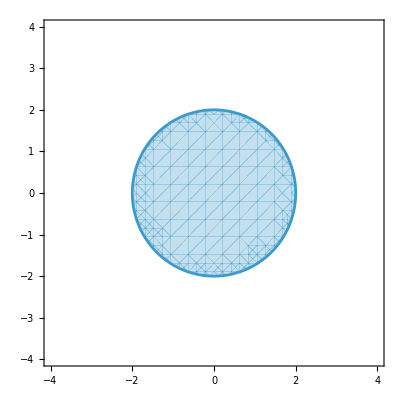

```mathematica
RegionPlot[Abs[z]≤2,{x,-4,4},{y,-4,4}]
```

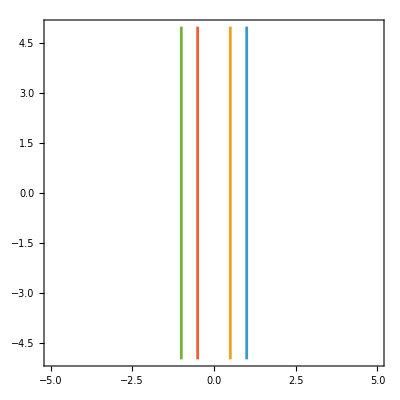

```mathematica
S1=ContourPlot[{Re[z]==1,Re[z]==1/2,Re[z]==-1,Re[z]==-1/2},{x,-5,5},{y,-5,5}]
```

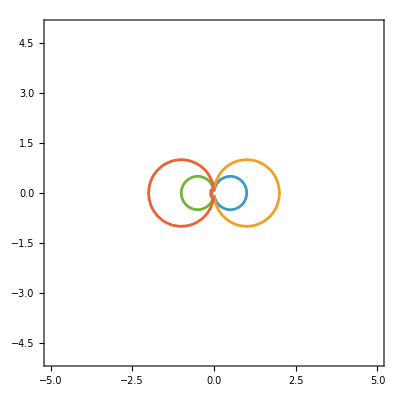

```mathematica
S2=ContourPlot[{Re[1/z]==1,Re[1/z]==1/2,Re[1/z]==-1,Re[1/z]==-1/2},{x,-5,5},{y,-5,5}]
```

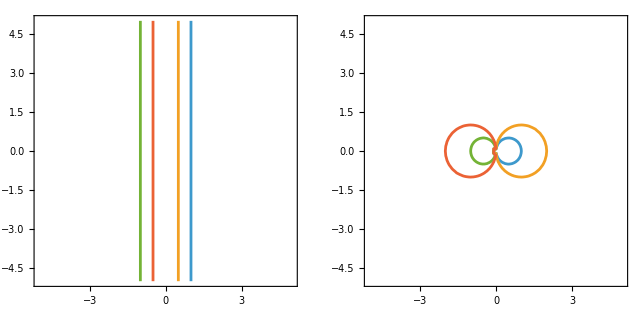

```mathematica
GraphicsRow[{S1,S2}]
```

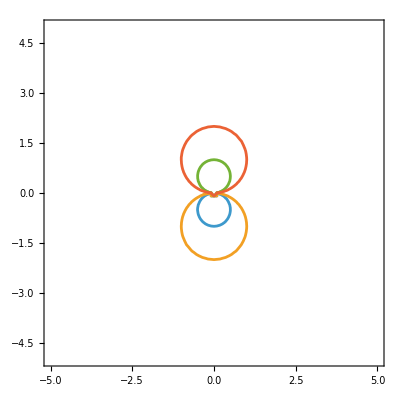

```mathematica
S3=ContourPlot[{Im[1/z]==1,Im[1/z]==1/2,Im[1/z]==-1,Im[1/z]==-1/2},{x,-5,5},{y,-5,5},Axes->True]
```

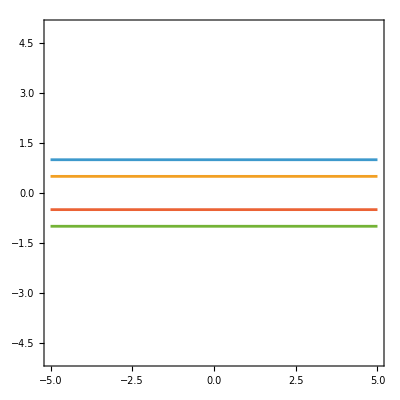

```mathematica
S4=ContourPlot[{Im[z]==1,Im[z]==1/2,Im[z]==-1,Im[z]==-1/2},{x,-5,5},{y,-5,5},Axes->True]
```

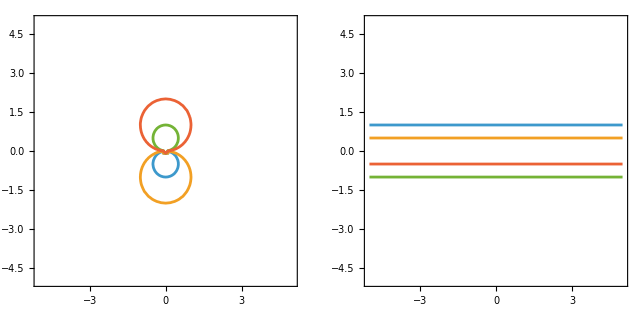

```mathematica
GraphicsRow[{S3,S4}]
```

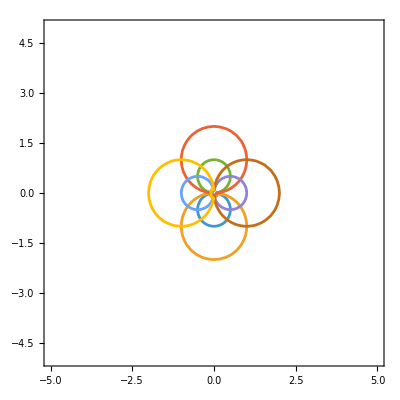

```mathematica
S5=ContourPlot[{Im[1/z]==1,Im[1/z]==1/2,Im[1/z]==-1,Im[1/z]==-1/2,Re[1/z]==1,Re[1/z]==1/2,Re[1/z]==-1,Re[1/z]==-1/2},{x,-5,5},{y,-5,5},Axes->True]
```

Practical 8

Find a parametrization of the polygonal path C = C1 + C2 + C3 from –1 + i to 3 – i, where C1 is the line from: –1 + i to –1, C2 is the line from: –1 to 1 + i and C3 is the line from          
1 + i to 3 – i.  Make a plot of this path.

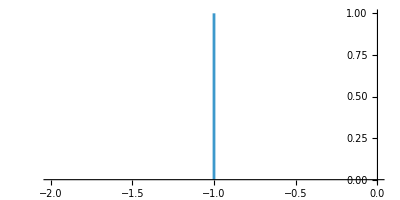

```mathematica
C1=ParametricPlot[{-1,1-t},{t,0,1},Axes->True]
```

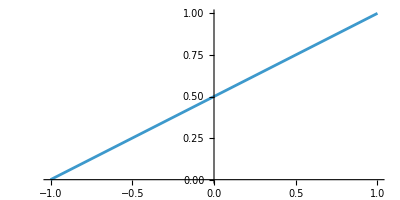

```mathematica
C2=ParametricPlot[{-1+2t,t},{t,0,1},Axes->True]
```

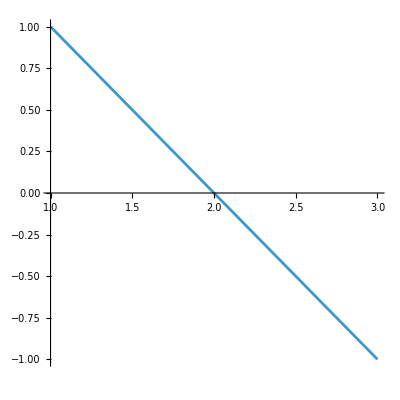

```mathematica
C3=ParametricPlot[{1+2t,1-2t},{t,0,1},Axes->True]
```

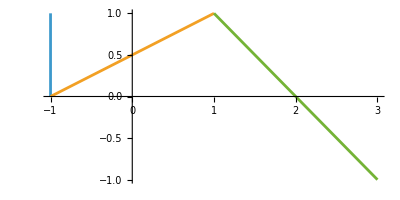

```mathematica
ParametricPlot[{{-1,1-t},{-1+2t,t},{1+2t,1-2t}},{t,0,1},Axes->True]
```

Practical 9

Plot the line segment ‘L’ joining the point A = 0 to B = 2 + 𝜋/4 of  ∫ 𝑒^𝑧𝑑𝑧.

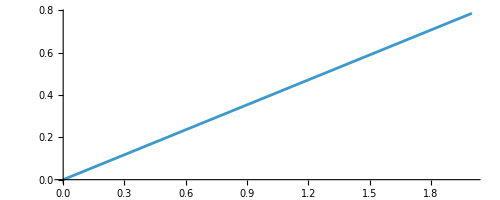

```mathematica
ParametricPlot[{2*t,Pi*t/4},{t,0,1}]
```

```mathematica
f[z_]:=Exp[z]
g[t_]:=2*t+ⅈ*Pi*t/4
a=Integrate[f[g[t]]*g'[t],{t,0,1}]
```

-1+(-1)^(1/4) ⅇ^2

```mathematica
N[a]
```

4.22485+5.22485 ⅈ

Practical 10

Evaluate ∫ 1/ 𝑧−2 𝑑𝑧, where C is the upper semicircle with radius 1 centered at z = 2 oriented in a positive direction.

```mathematica
f[z_]:=1/(z-2)
g[t_]:=2+Exp[ⅈ*t]
b=Integrate[f[g[t]]*g'[t],{t,0,Pi}]
```

ⅈ π

```mathematica
N[b]
```

0.+3.14159 ⅈ

Practical 11 (a)

Show that ∫ 𝑧𝑑z =∫ 𝑧𝑧𝑑𝑑𝑧𝑧 =4+2𝑖, where C1 is the line segment from –1 – i to 3 + i   and C2 is the portion of the parabola x = y2 + 2y joining  –1 – i to 3 + i.  Make plots of two contours C1 and C2 joining –1 – i to 3 + i .

```mathematica
f[z_]:=z
g[t_]:=-1+4t+(-1+2*t)ⅈ
c=Integrate[f[g[t]]*g'[t],{t,0,1}]
```

4+2 ⅈ

```mathematica
N[c]
```

4.+2. ⅈ

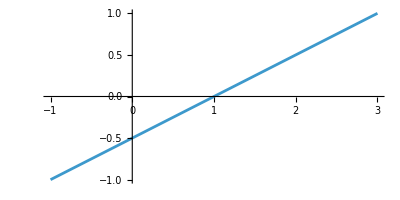

```mathematica
ParametricPlot[{-1+4t,-1+2t},{t,0,1}]
```

Practical 11 (b)

```mathematica
f[z_]:=z
h[t_]:=t^2+2t+ⅈ*t
d=Integrate[f[h[t]]*h'[t],{t,-1,1}]
```

4+2 ⅈ

```mathematica
N[d]
```

4.+2. ⅈ

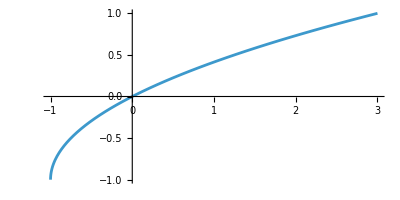

```mathematica
ParametricPlot[{t^2+2t,t},{t,-1,1}]
```

Practical 12

Use the ML inequality to show that  |∫ 1/ 𝑧^2+1 dz|<= 1/ 2√5
 , where C is the straight-line segment from 2 to 2 + i.  While solving, represent the distance from the point z to the 
points i and – i, respectively, i.e., |𝑧 − 𝑖| and |𝑧 + 𝑖| on the complex plane ℂ.

```mathematica
f[z_]:=1/(z^2+1)
g[t_]:=2+ⅈ*t
va1=Integrate[f[g[t]]*g'[t],{t,0,1}]
```

-ArcTan[2]+ArcTan[2+ⅈ]

```mathematica
t1=ComplexExpand[va1]
```

(3 π)/8-ArcTan[2]+ⅈ (-Log[2]/2+Log[8]/4)

```mathematica
N[Abs[t1]]
```

0.187249

```mathematica
N[1/2*Sqrt[5]]
```

1.11803

Practical 13 - Laurent Series

Find and plot three different Laurent series representations for the function:          
 𝑓(𝑧) = 3/ 2+𝑧−𝑧^2 , involving powers of z.

```mathematica
f[z_]:=3/(2+z-z^2)
Apart[f[z]](*used to give partial fractions*)
```

-1/(-2+z)+1/(1+z)

```mathematica
?Series
```

```mathematica
Series[f[z],{z,0,7}]
```

3/2-(3 z)/4+(9 z^2)/8-(15 z^3)/16+(33 z^4)/32-(63 z^5)/64+(129 z^6)/128-(255 z^7)/256+O[z]^8

```mathematica
Series[f[z],{z,Infinity,7}]
```

-3/z^2-3/z^3-9/z^4-15/z^5-33/z^6-63/z^7+O[1/z]^8

```mathematica
f1[z_]:=1/(1+z)
```

```mathematica
f2[z_]:=-1/(z-2)
```

```mathematica
t2=Series[f1[z],{z,Infinity,7}]
```

1/z-(1/z)^2+(1/z)^3-(1/z)^4+(1/z)^5-(1/z)^6+(1/z)^7+O[1/z]^8

```mathematica
s1=Normal[t2]
```

1/z^7-1/z^6+1/z^5-1/z^4+1/z^3-1/z^2+1/z

```mathematica
t3=Series[f2[z],{z,0,7}]
```

1/2+z/4+z^2/8+z^3/16+z^4/32+z^5/64+z^6/128+z^7/256+O[z]^8

```mathematica
s2=Normal[t3]
```

1/2+z/4+z^2/8+z^3/16+z^4/32+z^5/64+z^6/128+z^7/256

```mathematica
Print["The Laurent series expansion of the given function in the domain 1<|z|<2 is","...+",s1,"+",s2,"+..."]
```

The Laurent series expansion of the given function in the domain 1<|z|<2 is...+1/z^7-1/z^6+1/z^5-1/z^4+1/z^3-1/z^2+1/z+1/2+z/4+z^2/8+z^3/16+z^4/32+z^5/64+z^6/128+z^7/256+...

Practical 14

Locate the poles of  𝑓(𝑧) = 1/ 5𝑧^4+26𝑧^2+5
 and specify their order.

```mathematica
f[z_]:=1/(5*z^4+26*z^2+5)
```

```mathematica
Apart[f[z]]
```

-1/(24 (5+z^2))+5/(24 (1+5 z^2))

```mathematica
Solve[5*z^4+26*z^2+5==0,z]
```

{{z→-ⅈ/(√5)},{z→ⅈ/(√5)},{z→-ⅈ √5},{z→ⅈ √5}}

```mathematica
Series[f[z],{z,ⅈ/Sqrt[5],7}]
```

-(ⅈ √5)/(48 (z-ⅈ/(√5)))+25/576+(185 ⅈ √5 (z-ⅈ/(√5)))/6912-(5225 (z-ⅈ/(√5))^2)/82944-(32725 ⅈ √5 (z-ⅈ/(√5))^3)/995328+(965125 (z-ⅈ/(√5))^4)/11943936+(5848625 ⅈ √5 (z-ⅈ/(√5))^5)/143327232-(174670625 (z-ⅈ/(√5))^6)/1719926784-(1050548125 ⅈ √5 (z-ⅈ/(√5))^7)/20639121408+O[z-ⅈ/(√5)]^8

```mathematica
Residue[f[z],{z,ⅈ/Sqrt[5]}]
```

-(ⅈ √5)/48

Observation - Pole of order 1 and residue = -i/Sqrt[5], complete practical 14

Practical 15

Locate the zeros and poles of  𝑔(𝑧) = 𝜋cot(𝜋𝑧)/𝑧^2  and determine  their order.Also justify that Res(g,0)=-π^2/3.

```mathematica
g[z]:=Pi*Cos[Pi*z]/(z^2*Sin [Pi*z])
```

```mathematica
Series[g[z],{z,0,5}]
```

1/z^3-π^2/(3 z)-(π^4 z)/45-(2 π^6 z^3)/945-(π^8 z^5)/4725+O[z]^6

```mathematica
Residue[g[z],{z,0}]
```

-π^2/3

```mathematica
Series[g[z],{z,2,7}]
```

1/(4 (z-2))-1/4+1/48 (9-4 π^2) (z-2)+(-1/(8 π)+π/12) π (z-2)^2+π (5/(64 π)-π/16-π^3/180) (z-2)^3+π (-3/(64 π)+π/24+π^3/180) (z-2)^4+π (7/(256 π)-(5 π)/192-π^3/240-π^5/1890) (z-2)^5+π (-1/(64 π)+π/64+π^3/360+π^5/1890) (z-2)^6+π (9/(1024 π)-(7 π)/768-π^3/576-π^5/2520-π^7/18900) (z-2)^7+O[z-2]^8

```mathematica
Residue[g[z],{z,2}]
```

1/4

Pole 2 is of order 1